```mathematica
This is a brief tutorial on phylogenetic tree inference using the perfect phylogeny model
Authors: Ray Surjyendu and José Bento. Contact info <surjray@gmail.com>

* layout of the presentation
- What is our problem? (ans: get a tree from frequency of mutations per position)
- What is main assumption we will make when solving this problem? (ans: perfect phylogeny model)
- What are the different components of the perfect phylonegy model? (ans: T, M and F)
- What is the main equation of this model (ans: F = M + TF)
- How can we use this model to learn a tree (ans: brute force & ILP)
- What is the main idea behind bruteforce? (ans: Prufer, convex optimization, GPU).
- What is the main idea behind ILP? (ans: tree = set of linear constraints that select best subgraph from a directed graph of potential parental relations).
```

a brief inference is model on perfect phylogenetic phylogeny the This tree tutorial using

Syntax::sntxi: Incomplete expression; more input is needed .

(0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

2

{2->1,2->3,3->4}

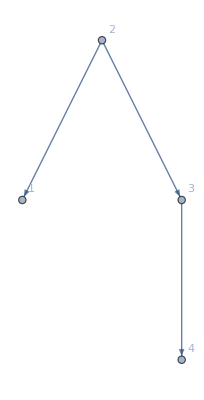

(0 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 0)

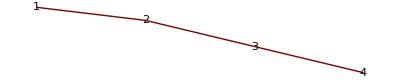

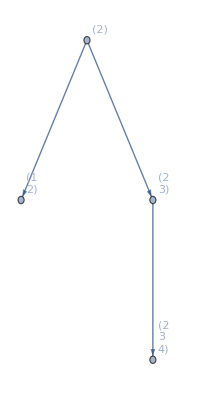

```mathematica
(*T is a tree*)
T = {{0,1,0,0},{0,0,0,0},{0,1,0,0},{0,0,1,0}}//Transpose;
T//MatrixForm
RootNode=Position[Total[T],0][[1,1]]
NumNodes=Dimensions[T][[1]];
NumEdges=NumNodes-1;
ParentChild=Position[T,1];
ParentChild=Table[ParentChild[[i,1]]->ParentChild[[i,2]],{i,1,NumEdges}]
TreeGraph[ParentChild,VertexLabels->"Name"]
AdjMat=T+Transpose[T];
AdjMat//MatrixForm
GraphPlot[T,VertexLabeling->True]
U=Inverse[IdentityMatrix[NumNodes]-T];
 AncesterList=Flatten/@(Position[#,1]&/@(U//Transpose));
TreeGraph[ParentChild,VertexLabels->Table[i->(AncesterList[[i]]//MatrixForm),{i,NumNodes}]]
```

{0.05,0.5,0.3,0.15}

1.

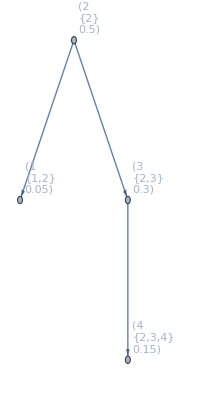

```mathematica
(*M is the frequency of each mutant on the population*)
M = {0.05,0.5,0.3,0.15}
M//Total
TreeGraph[ParentChild,VertexLabels->Table[i->({i,(AncesterList[[i]]),M[[i]]}//MatrixForm),{i,NumNodes}]]
```

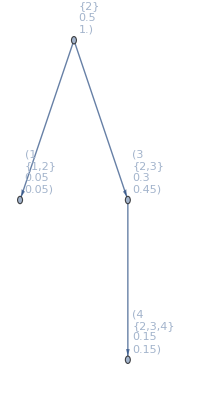

```mathematica
(*F is the frequency per position count*)
F=∑_(i=0)^∞ MatrixPower[T,i].M;
F=Inverse[IdentityMatrix[NumNodes]-T].M;(*F = (I - T)^-1 M => (I - T) F = M => F = M + T F*)
TreeGraph[ParentChild,VertexLabels->Table[i->({i,(AncesterList[[i]]),M[[i]],F[[i]]}//MatrixForm),{i,NumNodes}]]
```

```mathematica
(*In practice, ther is actually multiple samples. In our case, over time*)
NumSamples =10;
Mt=Partition[RandomReal[{0,1},NumSamples*NumNodes],NumSamples];
Mt=Mt.DiagonalMatrix[1/(Mt//Total)];
Ft=Inverse[IdentityMatrix[NumNodes]-T].Mt;
Manipulate[
{TreeGraph[ParentChild,VertexSize->Table[i->Sqrt[Mt[[i]][[t]]],{i,NumNodes}]],TreeGraph[ParentChild,VertexSize->Table[i->Sqrt[Ft[[i]][[t]]],{i,NumNodes}]]},{t,1,NumSamples,1}]
```

```mathematica
(*How do we get T and M from F*)
```

```mathematica
(*First idea...brute force*)
(*For the ground truth T, we we should have F = M + T F  equiv  (F - M - T F)^2 = 0. Therefore, given some data we look for min_(over all Tguess) min_Mguess ( (F - Tguess F) - Mguess )^2 *)
(*For a fixed T, the search over M is basically a convex optimization problem. The search over T needs to be done brute force*)
GetTreeFromTuple[CurrentTuple_,NumNodes_]:=Module[{i,j,Degrees,Tree,vali,LastTwo},
Degrees=1+BinCounts[CurrentTuple,{1,NumNodes+1,1}];
Tree=Table[0,{i,NumNodes},{j,NumNodes}];
For[i=1,i≤NumNodes-2,i++,{
vali=CurrentTuple[[i]];
For[j=1,j≤NumNodes,j++,{
If[Degrees[[j]]==1,{
Tree[[j,CurrentTuple[[i]]]]=1;
Tree[[CurrentTuple[[i]],j]]=1;
Degrees[[vali]]=Degrees[[vali]]-1;
Degrees[[j]]=Degrees[[j]]-1;
Break[];
}];
}];
}];
LastTwo=Position[Degrees,1]//Flatten;
Tree[[LastTwo[[1]],LastTwo[[2]]]]=1;
Tree[[LastTwo[[2]],LastTwo[[1]]]]=1;
Tree
];
GetTreeMatrixFromAdj[adjmat_,startnode_,NumNodes_]:=Module[{s,supp,i,sbf},
s=Table[If[i==startnode,1,0],{i,NumNodes}];
supp=0;
For[i=1,i≤NumNodes,i++,{
sbf=s;
s=If[#>0,1,0]&/@(s+adjmat.s);
supp=supp+KroneckerProduct[s,s-sbf];
}];
supp*adjmat
];
AllTuples=Tuples[Table[i,{i,NumNodes}],NumNodes-2];
Manipulate[
T=GetTreeMatrixFromAdj[GetTreeFromTuple[AllTuples[[i]],NumNodes],RootNode,NumNodes];
l=GraphDiameter[AdjacencyGraph[T+Transpose[T]]];
AdjacencyGraph[T,VertexLabels->Automatic],{i,1,NumNodes^(NumNodes-2),1}]
```

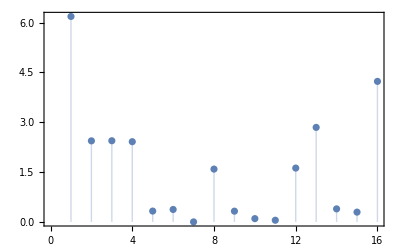

-Graphics-

```mathematica
treecosts=Table[
T=GetTreeMatrixFromAdj[GetTreeFromTuple[AllTuples[[i]],NumNodes],RootNode,NumNodes];
Msolve=Table[Subscript[m, i,j],{i,1,NumNodes},{j,1,NumSamples}];
MsolveV=Msolve//Flatten;
ModelErrorV=(Ft-Msolve-T.Ft)//Flatten;
{treecost,sol}=FindMinimum[{ModelErrorV.ModelErrorV,Thread[MsolveV≥0],Thread[Total[Msolve]==1]},MsolveV];
treecost,
{i,1,NumNodes^(NumNodes-2)}];
ListPlot[treecosts,Frame->True,Filling->Bottom]
bestix=Ordering[treecosts,1][[1]];
T=GetTreeMatrixFromAdj[GetTreeFromTuple[AllTuples[[bestix]],NumNodes],RootNode,NumNodes];
AdjacencyGraph[T,VertexLabels->Automatic]
```

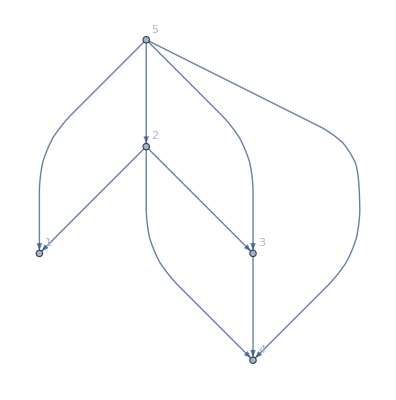

```mathematica
(*Build ancestry graph and extended ancestry graph*)
A=Table[And@@Thread[Ft[[i,;;]]>=Ft[[j,;;]]],{i,NumNodes},{j,NumNodes}]/.{True->1,False->0};
A=A-IdentityMatrix[NumNodes];
Aext =({{A, 0}, {1, 0}})//ArrayFlatten;
Aext//AdjacencyGraph[#,VertexLabels->Automatic]&
```

```mathematica
(*Here we solve the model via an Integer Linear Program*)
(*First, we give a formulation that assumes no noise in the measurement process works*)
Remove[x];
allvariables=Subscript[x, #[[1]],#[[2]]]&/@Position[Aext,1];
objective=(Subscript[x, #[[1]],#[[2]]]&/@Position[Aext,1]//Total);
rootsumcondition=(Subscript[x, NumNodes+1,#[[1]]]&/@Position[Aext[[NumNodes+1,;;]],1]//Total)==1;
flowconditionperedge[a_,b_]:=Subscript[x, a,b]≤Total[(Subscript[x, #[[1]],a]&/@Position[Aext[[;;,a]],1])];
flowcondition=flowconditionperedge[#[[1]],#[[2]]]&/@Position[A,1];
onefatherconditionpernode[a_]:=Total[(Subscript[x, #[[1]],a]&/@Position[Aext[[;;,a]],1])]≤1;
onefathercondition=onefatherconditionpernode/@Table[i,{i,NumNodes}];
valuesconditionpernodeandsample[f_,a_,p_]:=Total[(f[[#[[1]],p]]*Subscript[x, a,#[[1]]]&/@Position[Aext[[a,;;]],1])]≤Total[(f[[a,p]]*Subscript[x, #[[1]],a]&/@Position[Aext[[;;,a]],1])];
valuescondition[f_]:=valuesconditionpernodeandsample[f,#[[1]],#[[2]]]&/@Flatten[Table[{i,t},{i,NumNodes},{t,NumSamples}],1];
integercondition=#∈Integers&/@allvariables;
positivecondition=#≥0&/@allvariables;
maxonecondition=#≤1&/@allvariables;
fullproblem=Join[{objective},{rootsumcondition},flowcondition,onefathercondition,valuescondition[Ft],integercondition,positivecondition,maxonecondition];
fullproblem//MatrixForm
solILP=FindMaximum[fullproblem,allvariables];
GuessedRoot=Position[Table[Subscript[x, NumNodes+1,i],{i,NumNodes}]/.solILP[[2]],1][[1,1]];
GuessedTree=(Table[Subscript[x, i,j],{i,NumNodes},{j,NumNodes}]*A)/.solILP[[2]];
AdjacencyGraph[GuessedTree,VertexLabels->Automatic]
```

(x_(2,1)+x_(2,3)+x_(2,4)+x_(3,4)+x_(5,1)+x_(5,2)+x_(5,3)+x_(5,4)
x_(5,1)+x_(5,2)+x_(5,3)+x_(5,4)==1
x_(2,1)≤x_(5,2)
x_(2,3)≤x_(5,2)
x_(2,4)≤x_(5,2)
x_(3,4)≤x_(2,3)+x_(5,3)
x_(2,1)+x_(5,1)≤1
x_(5,2)≤1
x_(2,3)+x_(5,3)≤1
x_(2,4)+x_(3,4)+x_(5,4)≤1
0≤0.322603 x_(2,1)+0.322603 x_(5,1)
0≤0.430002 x_(2,1)+0.430002 x_(5,1)
0≤0.097531 x_(2,1)+0.097531 x_(5,1)
0≤0.258183 x_(2,1)+0.258183 x_(5,1)
0≤0.23621 x_(2,1)+0.23621 x_(5,1)
0≤0.334863 x_(2,1)+0.334863 x_(5,1)
0≤0.238234 x_(2,1)+0.238234 x_(5,1)
0≤0.169297 x_(2,1)+0.169297 x_(5,1)
0≤0.0286518 x_(2,1)+0.0286518 x_(5,1)
0≤0.125566 x_(2,1)+0.125566 x_(5,1)
0.322603 x_(2,1)+0.666646 x_(2,3)+0.266086 x_(2,4)≤1. x_(5,2)
0.430002 x_(2,1)+0.409764 x_(2,3)+0.0403938 x_(2,4)≤1. x_(5,2)
0.097531 x_(2,1)+0.848697 x_(2,3)+0.400092 x_(2,4)≤1. x_(5,2)
0.258183 x_(2,1)+0.328551 x_(2,3)+0.0996058 x_(2,4)≤1. x_(5,2)
0.23621 x_(2,1)+0.69591 x_(2,3)+0.34829 x_(2,4)≤1. x_(5,2)
0.334863 x_(2,1)+0.413557 x_(2,3)+0.201779 x_(2,4)≤1. x_(5,2)
0.238234 x_(2,1)+0.33323 x_(2,3)+0.0871209 x_(2,4)≤1. x_(5,2)
0.169297 x_(2,1)+0.423937 x_(2,3)+0.387426 x_(2,4)≤1. x_(5,2)
0.0286518 x_(2,1)+0.803968 x_(2,3)+0.293486 x_(2,4)≤1. x_(5,2)
0.125566 x_(2,1)+0.625985 x_(2,3)+0.267678 x_(2,4)≤1. x_(5,2)
0.266086 x_(3,4)≤0.666646 x_(2,3)+0.666646 x_(5,3)
0.0403938 x_(3,4)≤0.409764 x_(2,3)+0.409764 x_(5,3)
0.400092 x_(3,4)≤0.848697 x_(2,3)+0.848697 x_(5,3)
0.0996058 x_(3,4)≤0.328551 x_(2,3)+0.328551 x_(5,3)
0.34829 x_(3,4)≤0.69591 x_(2,3)+0.69591 x_(5,3)
0.201779 x_(3,4)≤0.413557 x_(2,3)+0.413557 x_(5,3)
0.0871209 x_(3,4)≤0.33323 x_(2,3)+0.33323 x_(5,3)
0.387426 x_(3,4)≤0.423937 x_(2,3)+0.423937 x_(5,3)
0.293486 x_(3,4)≤0.803968 x_(2,3)+0.803968 x_(5,3)
0.267678 x_(3,4)≤0.625985 x_(2,3)+0.625985 x_(5,3)
0≤0.266086 x_(2,4)+0.266086 x_(3,4)+0.266086 x_(5,4)
0≤0.0403938 x_(2,4)+0.0403938 x_(3,4)+0.0403938 x_(5,4)
0≤0.400092 x_(2,4)+0.400092 x_(3,4)+0.400092 x_(5,4)
0≤0.0996058 x_(2,4)+0.0996058 x_(3,4)+0.0996058 x_(5,4)
0≤0.34829 x_(2,4)+0.34829 x_(3,4)+0.34829 x_(5,4)
0≤0.201779 x_(2,4)+0.201779 x_(3,4)+0.201779 x_(5,4)
0≤0.0871209 x_(2,4)+0.0871209 x_(3,4)+0.0871209 x_(5,4)
0≤0.387426 x_(2,4)+0.387426 x_(3,4)+0.387426 x_(5,4)
0≤0.293486 x_(2,4)+0.293486 x_(3,4)+0.293486 x_(5,4)
0≤0.267678 x_(2,4)+0.267678 x_(3,4)+0.267678 x_(5,4)
x_(2,1)∈Integers
x_(2,3)∈Integers
x_(2,4)∈Integers
x_(3,4)∈Integers
x_(5,1)∈Integers
x_(5,2)∈Integers
x_(5,3)∈Integers
x_(5,4)∈Integers
x_(2,1)≥0
x_(2,3)≥0
x_(2,4)≥0
x_(3,4)≥0
x_(5,1)≥0
x_(5,2)≥0
x_(5,3)≥0
x_(5,4)≥0
x_(2,1)≤1
x_(2,3)≤1
x_(2,4)≤1
x_(3,4)≤1
x_(5,1)≤1
x_(5,2)≤1
x_(5,3)≤1
x_(5,4)≤1)

-Graphics-